```mathematica
Maximize[{0.89(a1+p1+c1+w1)+1.1(a2+p2+c2+w2)+1.8(a3+p3+c3+w3)-0.45(a1+a2+a3)-0.55(p1+p2+p3)-0.7(c1+c2+c3)-0.5(w1+w2+w3),
c1≤0.2(a1+p1+c1+w1)&&
w1≥0.4(a1+p1+c1+w1)&&
p1≤0.25(a1+p1+c1+w1)&&
c2≤0.35(a2+p2+c2+w2)&&
a2≥0.25(a2+p2+c2+w2)&&
c3≥0.3(a3+p3+c3+w3)&&
c3≤0.5(a3+p3+c3+w3)&&
a3≥0.3(a3+p3+c3+w3)&&
a1+a2+a3≤2000&&
p1+p2+p3≤4000&&
c1+c2+c3≤5000&&
w1+w2+w3≤3000&&
a1≥0&&
a2≥0&&
a3≥0&&
p1≥0&&
p2≥0&&
p3≥0&&
c1≥0&&
c2≥0&&
c3≥0&&
w1≥0&&
w2≥0&&
w3≥0
},{a1,a2,a3,p1,p2,p3,c1,c2,c3,w1,w2,w3}]
```

{10069.7,{a1→0.,a2→0.,a3→2000.,p1→1363.64,p2→0.,p3→2636.36,c1→1090.91,c2→0.,c3→2030.3,w1→3000.,w2→0.,w3→0.}}

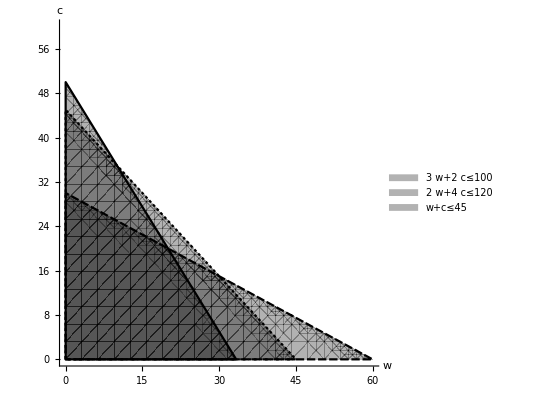

```mathematica
RegionPlot[{3w+2c≤100,2w+4c≤120,w+c≤45},
{w,0,60},{c,0,60},
PlotLegends->Placed["Expressions",{0.9,0.9}],
PlotRange->Full,
Axes->True,Frame->None,
AxesLabel->{w,c},
PlotTheme->"Monochrome"]
```

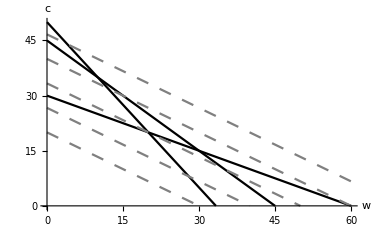

```mathematica
Plot[{(100-3w)/2,(120-2w)/4,45-w,(6000-200w)/300,(8000-200w)/300,(10000-200w)/300,(12000-200w)/300,(14000-200w)/300},{w,0,60},
PlotRange->{0,50},
PlotStyle->{Black,Black,Black,{Gray,Dashing@Medium},{Gray,Dashing@Medium},{Gray,Dashing@Medium},{Gray,Dashing@Medium},{Gray,Dashing@Medium}},
AxesLabel->{w,c}]
```

```mathematica
f[x_,y_]:=200x+300y
```

```mathematica
f[33.333,0]
```

6666.6

```mathematica
Minimize[{r,
r-(11-5c)≥0&&
r+(11-5c)≥0&&
r-(25-10c)≥0&&
r+(25-10c)≥0&&
r-(54-20c)≥0&&
r+(54-20c)≥0&&
r-(90-30c)≥0&&
r+(90-30c)≥0
},{r,c}]
```

{15/4,{r→15/4,c→23/8}}

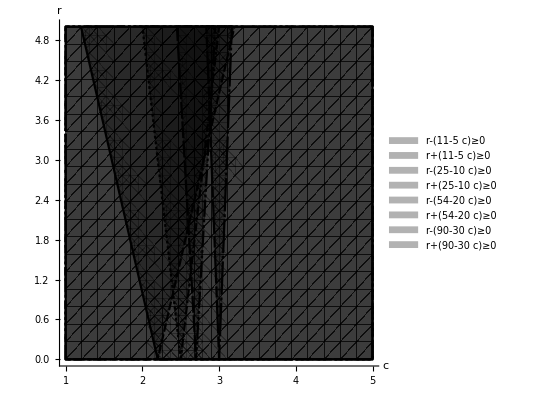

```mathematica
RegionPlot[{r-(11-5c)≥0,r+(11-5c)≥0,r-(25-10c)≥0, r+(25-10c)≥0,r-(54-20c)≥0, r+(54-20c)≥0,r-(90-30c)≥0,r+(90-30c)≥0},
{c,1,5},{r,0,5},
PlotLegends->Placed["Expressions",{0.9,0.9}],
Axes->True,Frame->None,
AxesLabel->{c,r},
PlotTheme->"Monochrome"]
```

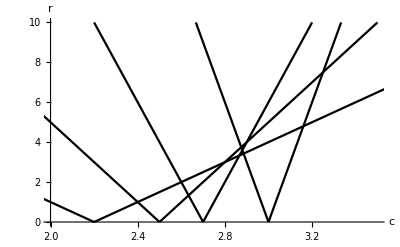

```mathematica
Plot[{(11-5c),-(11-5c), (25-10c),-(25-10c),(54-20c),-(54-20c),(90-30c),-(90-30c)},{c,0,5},
PlotRange->{{2,3.5},{0,10}},
PlotStyle->Black,
PlotLegends->"Expressions",
AxesLabel->{c,r}]
```

```mathematica
NSolve[-(25-10c)==-(54-20c)]
```

{{c→2.9}}

```mathematica
-(25-10 2.9)
```

4.

```mathematica
NSolve[-(25-10c)==(90-30c)]
```

{{c→2.875}}

```mathematica
-(25-10 2.875)
```

3.75

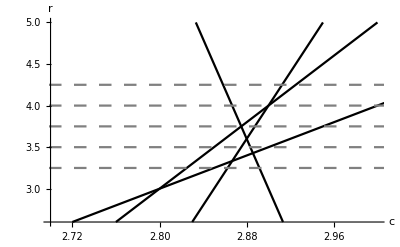

```mathematica
Plot[{(11-5c),-(11-5c), (25-10c),-(25-10c),(54-20c),-(54-20c),(90-30c),-(90-30c),3.25,3.5,3.75,4,4.25},{c,0,5},
PlotRange->{{2.7,3.0},{2.6,5}},
PlotStyle->{Black,Black,Black,Black,Black,Black,Black,Black,{Gray,Dashing@Medium},{Gray,Dashing@Medium},{Gray,Dashing@Medium},{Gray,Dashing@Medium},{Gray,Dashing@Medium}},
AxesLabel->{c,r}]
```